```mathematica
eV   =1;
MeV=10^6;
PeV=10^15;
pc  = 3.0857 * 10^18;
Gpc = 10^9 pc;
g=10^-3;
Subscript[m, ν] =0.01 eV;
(*Subscript[m, ϕ] =1 MeV;
Subscript[m, N]=10 MeV;*)
Subscript[E, ν] = 1 PeV;
Subscript[E, c] = (2 Subscript[m, ν] Subscript[E, ν])^(1/2);
Subscript[n, ν]=340; (*cm^-3*)
(* 1 eV = 8065.54429 cm^-1 *)
conv = 8065.54429;
```

```mathematica
sigma[X_,g_,mN_,mp_]:=(g^4 mN^2)/(32 π X^2)(1/(mN^2-mp^2+2X(X^2-mp^2)^(1/2))- 1/(2 X^2+mN^2-mp^2-2X(X^2-mp^2)^(1/2))-1/(mN^2-mp^2-2X(X^2-mp^2)^(1/2))+1/(2 X^2+mN^2-mp^2+2X(X^2-mp^2)^(1/2)) +1/(X^2+mN^2-mp^2)Log[((mp^2-mN^2-2 X^2+2X(X^2-mp^2)^(1/2))(mN^2-mp^2-2X(X^2-mp^2)^(1/2)))/((mp^2-mN^2-2 X^2-2X(X^2-mp^2)^(1/2))(mN^2-mp^2+2X(X^2-mp^2)^(1/2)))]);
```

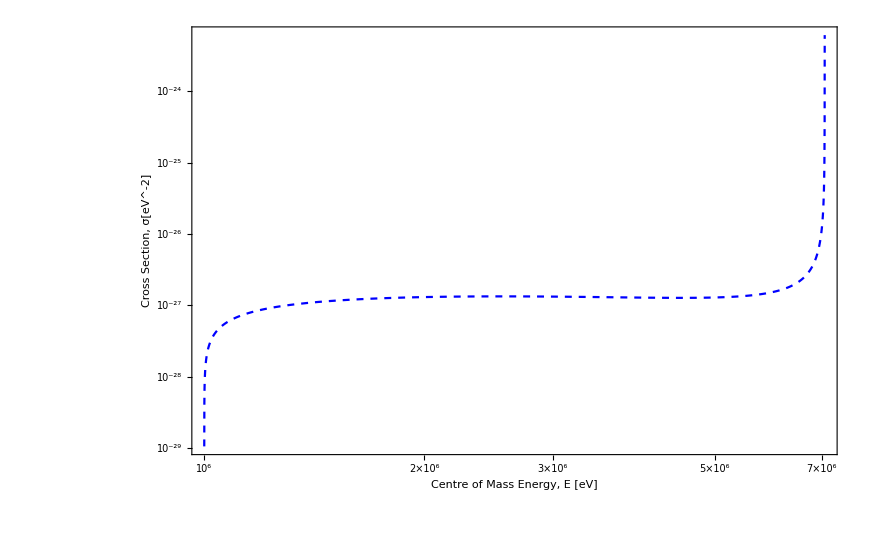

```mathematica
Subscript[m, ϕ] =1 MeV;
Subscript[m, N]=10 MeV;
LogLogPlot[-sigma[X, g, Subscript[m, N], Subscript[m, ϕ]],{X,0 MeV,100 Subscript[m, N]}, PlotPoints->200, PlotRange->All, GridLines->{{{Subscript[m, ϕ], Red},{Subscript[m, N], Red}},{}}, PlotStyle->{{Blue, Dashed}}, PlotTheme->"Scientific",FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Cross"," ","Section"}],","," ","σ[eV^-2]"}]],None},{RawBoxes[RowBox[{RowBox[{"Centre"," ","of"," ","Mass"," ","Energy"}],","," ","E", " ", "[eV]"}]],None}},PlotLabel->None,LabelStyle->{8,GrayLevel[0]}]
```

```mathematica
(*Subscript[σ, pev] = sigma[Subscript[E, c],g];
l=(conv^2)/(Subscript[n, ν] Subscript[σ, pev]); (*in cm*)
l / Gpc;
Subscript[d, b]=1.75 Gpc;*)
```